```mathematica
ed={2*θ''[t]*Sin[θ[t]/2]+(θ'[t])^2*Cos[θ[t]/2]-9.8*Cos[θ[t]/2]==0,2*ϕ''[t]*Sin[ϕ[t]/2]+(ϕ'[t])^2*Cos[ϕ[t]/2]-9.8*Cos[ϕ[t]/2]==0};
bdu={θ[0]==0.9,θ'[0]==0,ϕ[0]==1.8,ϕ'[0]==0};
sp3=NDSolve[{ed,bdu},{θ,ϕ},{t,0,50}]
```

{{θ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

```mathematica
theta[t_]=First[θ[t]/.sp3];
fai[t_]=First[ϕ[t]/.sp3];
x10[t_]=theta[t]-Sin[theta[t]];
z10[t_]=-1+Cos[theta[t]];
x20[t_]=fai[t]-Sin[fai[t]];
z20[t_]=-1+Cos[fai[t]];
Animate[Show[Graphics3D[{{Ball[{x10[t],0,z10[t]},0.1]},{Red,Ball[{x20[t],0,z20[t]},0.1]}},PlotRange->{{-1,2π+1},{-1,1},{-2.5,1}}],ParametricPlot3D[{u-Sin[u],0,-1+Cos[u]},{u,0,2π}]],{t,0,50},AnimationRunning->False,AnimationRate->1]
```

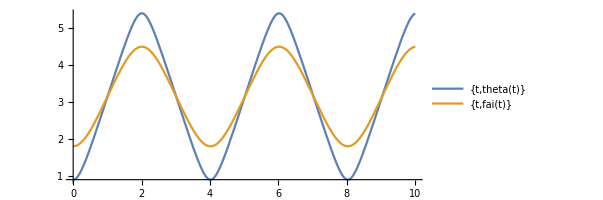

```mathematica
ParametricPlot[{{t,theta[t]},{t,fai[t]}},{t,0,10},PlotLegends->"Expressions"]
```

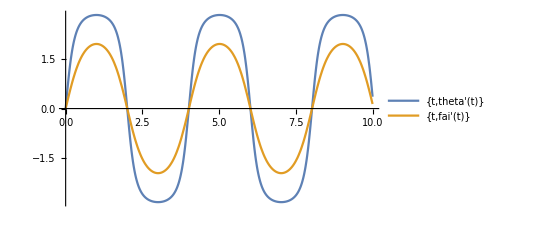

```mathematica
ParametricPlot[{{t,theta'[t]},{t,fai'[t]}},{t,0,10},PlotLegends->"Expressions"]
```